```mathematica
ClearAll["GraphPartition`*"]
SetDirectory[NotebookDirectory[]]
Import["GraphPartition.m"]
<< GraphPartition`
$Context
```

C:\Users\Chuqian\Desktop\research\graphPartitioning

Global`

C:\Users\Chuqian\Desktop\research\graphPartitioning

Global`

```mathematica
RandomGrid1[m_,n_,maxDist_:1, maxFanOut_:4]:= Module[{elist={},
vlist = Range[1,m*n],
vcoords= Flatten[Table[{i,j},{i,1,m},{j,1,n}],1],
 newE, neighbor},

Vertex1D[ij_] := (First[ij]-1)*n+Last[ij];
Neighbors[i_,j_,dist_] := Select[Flatten[Table[{i+di, j+dj},{di,-dist,dist},{dj,-dist,dist}],1],
1<=First[#]≤m && 1≤Last[#]≤n && #≠{i,j}&];
elist={};
Do[AppendTo[elist,{Vertex1D[{i,j}],Vertex1D[neighbor]}],
{i,1,m},{j,1,n},{neighbor, RandomChoice[Neighbors[i,j,maxDist],(*RandomInteger[{1,*)maxFanOut(*}]*)]}]
elist =DeleteDuplicates[elist,#1==#2||#1==Reverse[#2]& ];
(*Make sure that the result graph is connected*)
With[{components=#[[1]]&/@ConnectedComponents[elist]},
If[Length[components]>1,
elist=Join[elist, Map[{components[[1]], #}&,components[[2;;]]]];,
Nothing]];
newG=System`Graph[vlist,elist,VertexCoordinates->vcoords,
System`VertexWeight->Table[1/Length[vlist], Length[vlist]],System`EdgeWeight-> Table[1,Length[elist]],
System`VertexLabels->If[Max[m,n]<5,Automatic, None],
System`EdgeStyle->Directive[Opacity[0.5], Thick](*, EdgeShapeFunction->"Arrow"*)];
newG (*UndirectedGraph[newG]*)]
```

```mathematica
Graphics3D[{Arrow[{{0,0,0},d}],Arrow[{{0,0,0},v}],Arrow[{{0,0,0},len*dd}],Line[{len*dd,v}]},Axes->True]
```

```mathematica
sym=LineGraph[GridGraph[{5,5}]];
```

```mathematica
g = EdgeDelete[sym,EdgeList[sym][[RandomSample[Range[Length[EdgeList[sym]]],8]]]]
g=UndirectedGraph[#,VertexLabels->Automatic,VertexWeight->Table[1/V[#],V[#]], EdgeWeight->Automatic]&@g
```

```mathematica
basisVectors = FingerprintVectors[g,3]
```

```mathematica
iv = VectorPartition[basisVectors,V[g]/2, OptimizationOn->False,
				OptimizationObj-> (CriterionPartitionFunction[g,#,0.5]&)]
N[CriterionPartitionFunction[g,iv,0.5]]
dir=Normalize[Total[Table[basisVectors[[i]]*iv[[i]],{i,1,Length[iv]}]]]
```

```mathematica
(**)
ds=Table[
With[{iv=VectorMaxOnDirection[basisVectors,V[g]/2,{Cos[2*Pi/40*i],Sin[2*Pi/200*i]}, 
OptimizationOn->False,OptimizationObj->(CriterionPartitionFunction[g,#,0.5]&)]},
Total[Table[basisVectors[[i]]*iv[[i]],{i,1,Length[iv]}]]]
,{i,200}];
```

```mathematica
ListPlot[{basisVectors,ds,{Total[Table[basisVectors[[i]]*iv[[i]],{i,1,Length[iv]}]]}}]
ListPlot[basisVectors]
ListPlot[{Total[Table[basisVectors[[i]]*iv[[i]],{i,1,Length[iv]}]]}]
```

#### Idea - Mallow+Random Projection - KMeans + Linear combination of mean vectors?

```mathematica
(**)
newiv=VectorMaxOnDirection[basisVectors,V[g]/2,dir, 
OptimizationOn->False,OptimizationObj->(CriterionPartitionFunction[g,#,0.5]&)]
N[CriterionPartitionFunction[g,newiv,0.5]]
(*dir=Normalize[Total[Table[basisVectors[[i]]*newiv[[i]],{i,1,Length[iv]}]]]*)
```

```mathematica
newiv=VectorPartition[basisVectors,V[g]/2, 
OptimizationOn->False,OptimizationObj->(CriterionPartitionFunction[g,#,0.5]&),
Method->MallowProbe]
N[CriterionPartitionFunction[g,newiv,0.5]]
(*dir=Normalize[Total[Table[basisVectors[[i]]*newiv[[i]],{i,1,Length[iv]}]]]*)
```

```mathematica
ShowSpectralCut[g]
```

```mathematica
N[SpectralEdges[g,IncludeObj->True]]
```

```mathematica
{grounds, basis}= IsoperimetricBasis[g,3,GroundingPreviousMax]
```

Set::write: Tag Times in Null {{1,11},{1,3},{2,18},{2,11},{3,12},{3,2},{4,20},{4,12},{5,15},{5,15},{6,21},{6,15},{7,15},{7,5},{8,23},{8,22},{9,27},{9,25},{10,12},{10,19},{11,28},{11,29},{12,28},«6»,{15,21},{16,23},{16,8},{17,34},{17,1},{18,4},{18,3},{19,12},{19,2},{20,28},{20,35},{21,13},{21,28},{22,8},{22,37},{23,40},{23,5},{24,8},{24,40},{25,27},{25,33},«78»} is Protected.

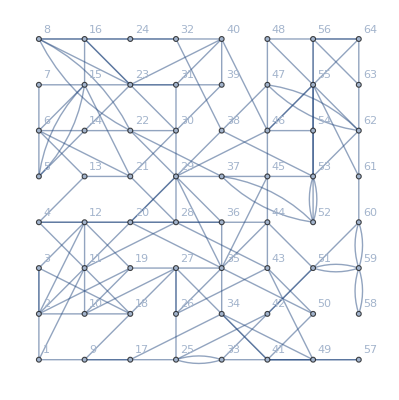

{{0.341753,0.483381},{0.2523,0.616495},{0.231809,0.69592},{0.249264,0.525392},{0.345269,0.145588},{0.319905,0.222309},{0.347921,0.164086},{0.306731,0.0498955},{0.351393,0.209129},{0.346407,0.377996},{0.363133,0.320373},{0.307813,0.478593},{0.289031,0.318561},{0.353735,0.209548},{0.33893,0.153146},{0.351826,0.0628024},{0.418674,0.404414},{0.0137264,1.17577},{0.333373,0.382382},{0.37484,0.0992077},{0.28628,0.178543},{0.483999,0.0244966},{0.34365,0.0825336},{0.342533,0.0502067},{0.30475,0.145246},{0.433852,0.1915},{0.386392,0.243574},{0.422082,0.243937},{0.424752,-0.0917603},{0.375921,0.167349},{0.364395,0.123671},{0.382257,-0.16835},{0.40166,0.176288},{0.48395,0.296008},{0.415329,0.0270044},{0.467225,0.19796},{0.359668,-0.253699},{0.401043,-0.428941},{0.336089,0.103865},{0.366692,0.0210799},{0.483913,0.264562},{0.372662,0.067802},{0.463954,0.204887},{0.439565,0.0966018},{0.473754,-0.459542},{0.435148,-0.284315},{0.265894,-0.332752},{0.427011,-0.415635},{0.554346,0.28766},{0.45828,0.175297},{0.431148,0.0975619},{0.29168,-0.407516},{0.569537,-1.34331},{0.449563,-0.623828},{0.477565,-0.612822},{0.46224,-0.500617},{0.524951,0.29083},{0.441683,0.0586788},{0.435861,0.0439597},{0.428931,-0.0390804},{0.459694,-0.341481},{0.384995,-0.598752},{0.460941,-0.401979},{0.449246,-0.393277}}

```mathematica
g =RandomGrid1[8,8,maxDist=2,maxFanOut=2];
(* EdgeDelete[sym,EdgeList[sym][[RandomSample[Range[Length[EdgeList[sym]]],8]]]];*)
g=UndirectedGraph[#,VertexLabels->Automatic,VertexWeight->Table[1/V[#],V[#]], EdgeWeight->Automatic]&@g
{grounds,basisVectors} = FingerprintVectors[g,2, GroundingRandom];
basisVectors = Re[basisVectors]
```

#### Melo

```mathematica
meloV=VectorPartition[basisVectors, V[g],OptimizationOn->True,OptimizationObj->(CriterionPartitionFunction[g,#,0.5]&)]
Norm[Total[basisVectors*meloV]]
N[CriterionPartitionFunction[g,meloV,0.5]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,1,1,0,0,0,0,0,0,1,1,1,1,0,0,0,1,1,1,1,1,0,0,0,0,1,1,1,1}

10.4945

46.1377

```mathematica
{0,1,1,1,1,1,0,1,0,1,0,1,1,1,0,1}
```

#### MeloProbe

```mathematica
meloProbeV=VectorPartition[basisVectors, V[g], Method->MeloProbe,OptimizationOn->True,OptimizationObj->(CriterionPartitionFunction[g,#,0.5]&)]
Norm[Total[basisVectors*meloProbeV]]
N[CriterionPartitionFunction[g,meloProbeV,0.5]]
```

{53,55,54,62,56,45,63,48,64,38,61,46,52,37,47,32,29,60,22,59,35,58,40,44,51,42,24,16,50,20,36,23,8,49,43,31,26,39,57,33,41,30,5,15,7,34,28,25,14,9,27,21,6,11,17,13,10,19,1,12,4,2,3,18}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,1,1,0,0,0,0,0,0,1,1,1,1,0,0,0,1,1,1,1,1,0,0,0,0,1,1,1,1}

10.4945

46.1377

```mathematica
meloProbe2V=VectorMaxOnDirection[basisVectors, V[g]/2, Normalize[Total[basisVectors*meloProbeV]](*+RandomReal[{0,1},3]*)]
Norm[Total[basisVectors*meloProbe2V]]
N[CriterionPartitionFunction[g,meloProbe2V,0.5]]
```

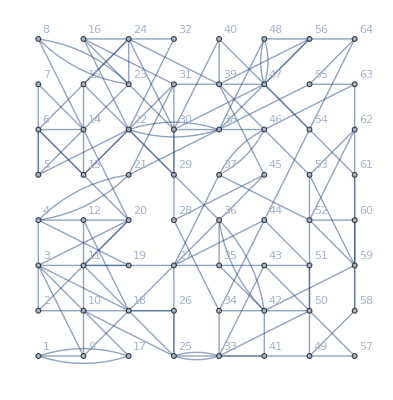
g-Graphics-

basis:{{0.293271,0.184907},{0.371679,0.240049},{0.393989,0.181115},{0.383691,-0.0877867},{0.226532,0.380609},{0.283802,0.194106},{0.225902,0.533471},{0.0107904,1.50774},{0.377384,0.197936},{0.372892,0.245871},{0.381841,0.219859},{0.389874,0.261087},{0.310507,-0.418511},{0.217162,0.632119},{0.338664,-0.197424},{0.257963,-0.487562},{0.49432,0.302572},{0.389798,0.2481},{0.392895,0.0737712},{0.340046,0.238946},{0.39171,-0.49349},{0.245097,-0.142721},{0.143219,0.883364},{0.316655,0.083153},{0.361467,0.195466},{0.377422,0.247884},{0.432325,0.151648},{0.386708,-0.101455},{0.380719,-0.311129},{0.414666,-0.479049},{0.366358,-1.58222},{0.255584,-0.288034},{0.43248,0.196264},{0.43186,0.104228},{0.304956,0.0985997},{0.231993,0.0306155},{0.373911,0.0608067},{0.424989,-0.270382},{0.394813,-0.039447},{0.429384,-0.182643},{0.525201,0.252522},{0.36981,0.112369},{0.459606,0.204285},{0.452977,0.0964857},{0.305489,0.0162399},{0.571451,-0.0642448},{0.488481,-0.546806},{0.589067,-0.449791},{0.501772,0.171846},{0.447167,0.171403},{0.469053,0.159502},{0.483759,0.10161},{0.475631,0.0992745},{0.470563,-0.0836486},{0.495917,-0.177784},{0.438797,-0.267474},{0.496458,0.255511},{0.526383,0.129976},{0.546799,0.0952794},{0.522468,0.0685885},{0.524823,-0.106726},{0.48375,0.127549},{0.533433,-0.0981799},{0.521218,-0.219003}}

meloN:24.4591

meloObj:69.4237

meloProbeN:24.4591

meloProbeObj:69.4237

Set::write: Tag Times in Null {{1,19},{1,10},{2,12},{2,11},{3,19},{3,12},{4,22},{4,19},{5,15},{5,20},{6,21},{6,12},{7,8},{7,6},{8,22},{8,6},{9,1},{9,19},{10,27},{10,2},{11,29},{11,3},«7»,{15,31},{16,15},{16,30},{17,33},{17,34},{18,9},{18,2},{19,9},{19,21},{20,37},{20,12},{21,38},{21,13},{22,29},{22,12},{23,16},{23,32},{24,38},{24,14},{25,27},{25,33},«78»} is Protected.

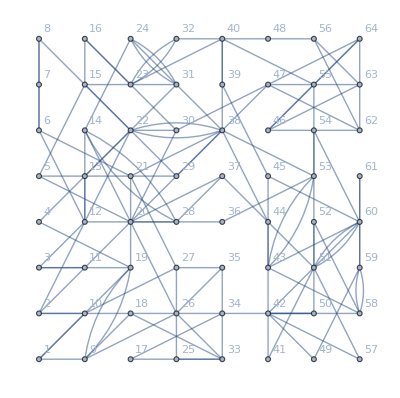
g-Graphics-

basis:{{0.303485,0.459154},{0.351754,0.523821},{0.390477,0.385882},{0.407062,0.345833},{0.399486,0.24211},{0.402093,0.303649},{0.41486,0.294035},{0.415941,0.276459},{0.211118,0.38645},{0.304395,0.523079},{0.391932,0.3817},{0.384559,0.308015},{0.378113,0.267163},{0.323905,0.193331},{0.393959,0.200644},{0.410083,0.14633},{0.111619,0.638028},{0.157222,0.437265},{0.383254,0.459971},{0.414699,0.250562},{0.381324,0.328123},{0.419184,0.223732},{0.395541,0.0553903},{0.44661,0.21822},{0.132589,0.75884},{0.199944,0.567896},{0.246259,0.578299},{0.36197,0.181895},{0.421877,0.227433},{0.429063,0.174993},{0.335396,0.182442},{0.654388,0.062004},{0.00723283,0.931419},{0.204319,0.336674},{0.155041,0.695192},{0.471324,0.0640045},{0.373684,0.0823939},{0.444662,0.12426},{0.525356,-0.170372},{0.506007,0.00526505},{0.379176,-0.268619},{0.413967,-0.351963},{0.57686,-0.399329},{0.435158,-0.109871},{0.533018,-0.35397},{0.483039,-0.0650318},{0.460598,0.0713869},{0.50449,0.00249025},{0.538224,-0.861932},{0.332428,-0.0732318},{0.332698,-0.193237},{0.367313,-0.212369},{0.516262,-0.130515},{0.455667,-0.201707},{0.499919,-0.0501452},{0.491287,-0.0082468},{0.379176,-0.268619},{0.33677,-0.38926},{0.650795,-1.37986},{0.485151,-0.500173},{0.573816,-0.936037},{0.47548,-0.0372164},{0.482204,0.0020235},{0.482681,-0.0182611}}

meloN:15.641

meloObj:44.1725

meloProbeN:15.641

meloProbeObj:44.1725

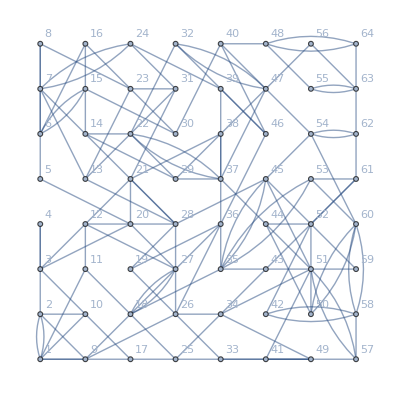
g-Graphics-

basis:{{0.339607,0.156367},{0.38526,0.191814},{0.40374,0.228462},{0.399181,0.218598},{0.343016,0.243721},{0.251215,0.182474},{0.277958,0.22934},{0.311098,0.246427},{0.471428,0.22827},{0.367115,0.18255},{0.406438,0.149195},{0.424196,0.196432},{0.394724,0.288072},{0.275619,0.262065},{0.362715,0.256749},{0.321685,0.209801},{0.398039,0.169453},{0.257287,0.0835996},{0.401841,0.176145},{0.398711,0.241183},{0.409667,0.267696},{0.267542,0.441254},{0.394759,0.310549},{0.333927,0.318838},{0.446149,0.0778673},{0.337164,0.148234},{0.429059,0.207932},{0.427727,0.21525},{0.308411,0.412877},{0.341763,0.173262},{0.469091,0.380228},{0.127286,0.577511},{0.441407,0.10661},{0.450278,0.0910746},{0.333438,0.025948},{0.327026,0.189655},{0.341415,0.674831},{0.339704,0.25644},{0.301337,0.419524},{0.331527,0.0363155},{0.492027,-0.00570823},{0.487377,-0.908284},{0.476497,-0.0103797},{0.497004,-0.513893},{0.404352,0.00295343},{0.219308,0.247985},{0.0129311,1.60389},{0.211894,0.0264576},{0.464358,0.0696319},{0.47355,-0.514574},{0.539949,0.0384389},{0.511096,-0.530131},{0.532517,-0.290767},{0.54378,-0.319361},{0.160295,0.0157467},{0.304348,0.138611},{0.513031,-0.254433},{0.470836,-1.10582},{0.238416,0.0145779},{0.876737,-1.03119},{0.577091,-0.200692},{0.548461,-0.310902},{0.25963,0.00386344},{0.34639,0.0368489}}

meloN:15.2759

meloObj:164.

meloProbeN:15.154

meloProbeObj:132.

```mathematica
For[i=1,i≤1,i+=1,
Module[{(*g,grounds,basisVectors,meloV, meloProbeV,meloN,meloObj,meloProbeN,meloProbeObj*)},
g =RandomGrid1[8,8,maxDist=2,maxFanOut=2];
(* EdgeDelete[sym,EdgeList[sym][[RandomSample[Range[Length[EdgeList[sym]]],8]]]];*)
g=UndirectedGraph[#,VertexLabels->Automatic,VertexWeight->Table[1/V[#],V[#]], EdgeWeight->Automatic]&@g;
{grounds,basisVectors} = FingerprintVectors[g,2, GroundingRandom];
basisVectors = Re[basisVectors];
meloV=VectorPartition[basisVectors, V[g],OptimizationOn->True,OptimizationObj->(CriterionPartitionFunction[g,#,0.5]&)];
meloN = Norm[Total[basisVectors*meloV]];
meloObj=N[CriterionPartitionFunction[g,meloV,0.5]];
meloProbeV=VectorPartition[basisVectors, V[g], Method->MeloProbe,OptimizationOn->True,OptimizationObj->(CriterionPartitionFunction[g,#,0.5]&)];
     meloProbeN=Norm[Total[basisVectors*meloProbeV]];
meloProbeObj=N[CriterionPartitionFunction[g,meloProbeV,0.5]];
(*If[meloObj== meloProbeObj,  
*)Print["g",g];
Print["basis:", basisVectors];
Print["meloN:", meloN];
Print["meloObj:", meloObj];
Print["meloProbeN:", meloProbeN];
Print["meloProbeObj:", meloProbeObj];]](*]*)
```

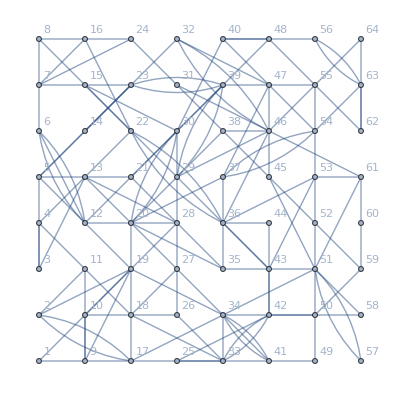
g-Graphics-

basis:{{0.430889,-1.31876},{0.292165,-0.198961},{0.464631,-0.179199},{0.444265,-0.174766},{0.414098,-0.135763},{0.300167,-0.0899418},{0.404306,-0.0555303},{0.380403,-0.052825},{0.480998,-0.455486},{0.496329,-0.272752},{0.414069,-0.251366},{0.395421,-0.122913},{0.506105,-0.165951},{0.360233,-0.0615136},{0.44351,-0.0584484},{0.429202,-0.0746321},{0.333493,-0.0912097},{0.409422,-0.115134},{0.391674,-0.392151},{0.296044,0.0413731},{0.457177,0.071206},{0.424672,-0.032617},{0.367348,-0.0560424},{0.386945,0.0252007},{0.642604,0.0187169},{0.462367,-0.115655},{0.455115,-0.0710184},{0.569143,-0.186518},{0.379562,0.0413224},{0.478033,-0.0971023},{0.3467,0.245075},{0.269829,0.0683821},{0.37911,0.015805},{0.310796,0.209334},{0.299331,0.376786},{0.420031,0.100128},{0.383354,0.112552},{0.176696,0.032254},{0.628677,0.0337121},{0.464137,-0.0984871},{0.420395,0.129147},{0.420047,0.158686},{0.414884,0.143706},{0.434752,0.0988481},{0.242415,0.62238},{0.381316,0.14876},{0.308341,0.247399},{0.457091,-0.112066},{0.353237,0.340486},{0.256654,0.612942},{0.0313257,1.34313},{0.253867,0.715033},{0.410469,0.335804},{0.491814,-0.0208407},{0.534285,0.154199},{0.400183,-0.102822},{0.0460383,1.31257},{0.240399,0.720349},{0.301834,0.619934},{0.365555,0.592943},{0.399852,0.62707},{0.399678,-0.0794927},{0.706987,-0.148862},{0.405209,0.00407511}}

meloN:18.897

meloObj:117.277

meloProbeN:23.7149

meloProbeObj:102.657

```mathematica
meloV=VectorPartition[basisVectors, V[g],OptimizationOn->True,OptimizationObj->(CriterionPartitionFunction[g,#,0.5]&)];
meloN = Norm[Total[basisVectors*meloV]];
meloObj=N[CriterionPartitionFunction[g,meloV,0.5]];
meloProbeV=VectorPartition[basisVectors, V[g], Method->MeloProbe,OptimizationOn->True,OptimizationObj->(CriterionPartitionFunction[g,#,0.5]&)];
     meloProbeN=Norm[Total[basisVectors*meloProbeV]];
meloProbeObj=N[CriterionPartitionFunction[g,meloProbeV,0.5]];
(*If[meloObj== meloProbeObj,  
*)Print["g",g];
Print["basis:", basisVectors];
Print["meloN:", meloN];
Print["meloObj:", meloObj];
Print["meloProbeN:", meloProbeN];
Print["meloProbeObj:", meloProbeObj];
```

```mathematica
N[SpectralEdges[g, IncludeObj->True]]
N[IsoperimetricEdges[g, IncludeObj->True]]
```

Less::nord: Invalid comparison with 5.91701+0.0314227 ⅈ attempted.

Less::nord: Invalid comparison with 5.91701-0.0314227 ⅈ attempted.

Less::nord: Invalid comparison with 5.91701+0.0314227 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

{128.,{4.<->20.,11.<->17.,11.<->3.,14.<->4.,22.<->39.,23.<->22.,28.<->18.,28.<->10.,29.<->44.,30.<->22.,32.<->38.,46.<->53.,48.<->55.,49.<->43.,49.<->34.,52.<->44.,53.<->35.,54.<->63.,55.<->39.,58.<->50.,58.<->57.,61.<->43.,63.<->64.,64.<->62.}}

{108.831,{5.<->14.,15.<->14.,15.<->14.,19.<->3.,25.<->35.,29.<->44.,33.<->27.,35.<->27.,37.<->54.,41.<->42.,43.<->37.,44.<->51.,45.<->30.,46.<->30.,47.<->31.,49.<->34.,50.<->44.,52.<->44.,55.<->61.,60.<->58.,62.<->61.,63.<->64.}}

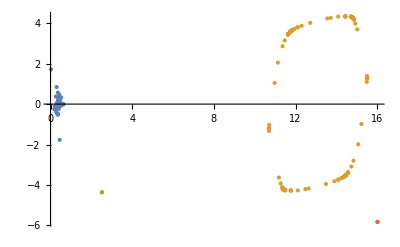

```mathematica
ListPlot[{basisVectors,ds,{Total[basisVectors*meloV]}, {Total[basisVectors*meloProbeV]}}]
```

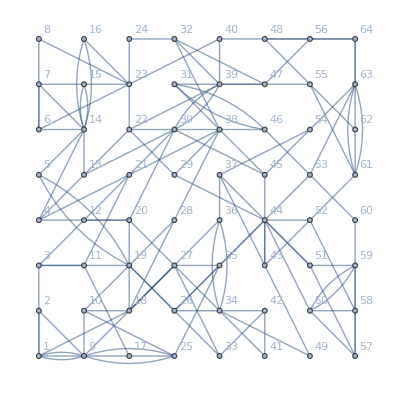

```mathematica
g
```

```mathematica
grounds
```

{21,16}

```mathematica
betterCounts=0;
worseCounts =0;
avgImp = 0;
T = 100;
For[ii=1,ii≤T,ii=ii+1,
Module[{(*g,grounds,basisVectors,meloV, meloProbeV,meloN,meloObj,meloProbeN,meloProbeObj*)},
g =RandomGrid1[10,10,maxDist=10,maxFanOut=2];
(* EdgeDelete[sym,EdgeList[sym][[RandomSample[Range[Length[EdgeList[sym]]],8]]]];*)
g=UndirectedGraph[#,VertexLabels->Automatic,VertexWeight->Table[1/V[#],V[#]], EdgeWeight->Automatic]&@g;
{grounds,basisVectors} = FingerprintVectors[g,3, GroundingRandom];
(*basisVectors = Re[basisVectors];*)
meloV=VectorPartition[basisVectors, V[g],OptimizationOn->True,OptimizationObj->(CriterionPartitionFunction[g,#,0.5]&)];
meloN = Norm[Total[basisVectors*meloV]];
meloObj=N[CriterionPartitionFunction[g,meloV,0.5]];
meloProbeV=VectorPartition[basisVectors, V[g], Method->MeloProbe,OptimizationOn->True,OptimizationObj->(CriterionPartitionFunction[g,#,0.5]&)];
     meloProbeN=Norm[Total[basisVectors*meloProbeV]];
meloProbeObj=N[CriterionPartitionFunction[g,meloProbeV,0.5]];
(*If[meloObj== meloProbeObj,  
*)(*Print["g",g];
Print["basis:", basisVectors];
Print["meloN:", meloN];*)
(*Print["meloObj:", meloObj];*)
(*Print["meloProbeN:", meloProbeN];*)
(*Print["meloProbeObj:", meloProbeObj];*)
 If[meloProbeObj<meloObj,betterCounts+=1, Nothing];
If[meloProbeObj>meloObj, worseCounts+=1, Nothing];
avgImp += (meloObj-meloProbeN)/meloObj;
]]
avgImp=avgImp/T
N[betterCounts/T]
N[worseCounts/T]
```

Set::write: Tag Times in Null {{1,61},{1,5},{2,65},{2,46},{3,73},{3,5},{4,54},{4,94},{5,75},{5,40},{6,88},{6,71},{7,62},{7,84},{8,45},{8,83},{9,67},{9,68},{10,32},{10,58},{11,40},{11,77},«7»,{15,54},{16,34},{16,57},{17,79},{17,69},{18,49},{18,63},{19,44},{19,71},{20,28},{20,49},{21,27},{21,51},{22,44},{22,13},{23,84},{23,2},{24,53},{24,40},{25,24},{25,31},«150»} is Protected.

Set::write: Tag Times in Null {{1,25},{1,76},{2,69},{2,40},{3,45},{3,21},{4,67},{4,79},{5,46},{5,9},{6,45},{6,32},{7,51},{7,46},{8,57},{8,95},{9,12},{9,19},{10,18},{10,29},{11,81},{11,24},«7»,{15,7},{16,37},{16,38},{17,92},{17,49},{18,24},{18,50},{19,26},{19,50},{20,42},{20,94},{21,97},{21,51},{22,90},{22,57},{23,2},{23,29},{24,72},{24,30},{25,11},{25,72},«150»} is Protected.

Set::write: Tag Times in Null {{1,21},{1,40},{2,56},{2,72},{3,94},{3,88},{4,50},{4,18},{5,58},{5,43},{6,44},{6,79},{7,54},{7,19},{8,27},{8,12},{9,61},{9,48},{10,9},{10,29},{11,56},{11,67},«7»,{15,36},{16,93},{16,56},{17,5},{17,70},{18,98},{18,70},{19,18},{19,91},{20,24},{20,51},{21,84},{21,15},{22,7},{22,21},{23,32},{23,85},{24,35},{24,88},{25,80},{25,50},«150»} is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

0.900802

0.29

0.